# Графика

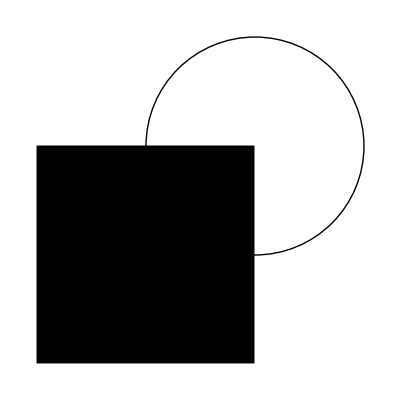

```mathematica
Graphics[{
Circle[{1,1},1],
Rectangle[{-1,-1},{1,1}],
}]
```

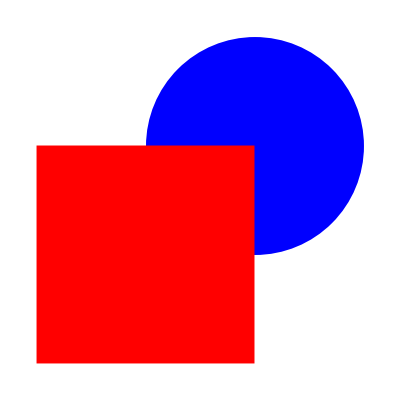

```mathematica
Graphics[{
Blue,Disk[{1,1},1],
Red,
Rectangle[{-1,-1},{1,1}],
}]
```

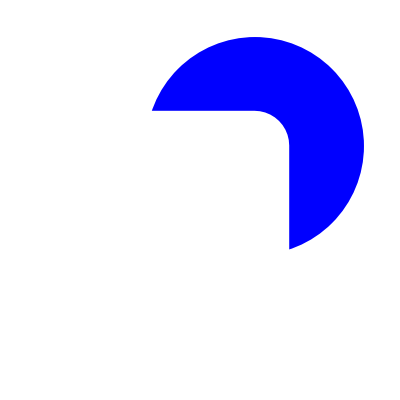

```mathematica
Graphics[{
Blue,Disk[{1,1},1],
White,EdgeForm[Directive[Thickness[.5],Dashed]],
Rectangle[{-1,-1},{1,1}],
}]
```

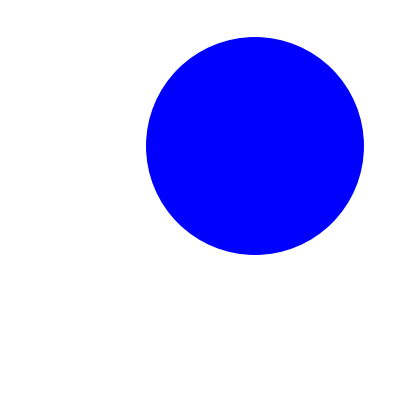

```mathematica
Graphics[{
White,EdgeForm[Directive[Thickness[.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],
Blue,Disk[{1,1},1]
}]
```

```mathematica
Graphics[{
White,EdgeForm[Directive[Thickness[.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],
Blue,{{{Disk[.2{1,1},.05]}}},
Thickness[.01],
Arrow[{.2{1,1},{.3,.4}}]
}]
```

-Graphics-

# Цвета

```mathematica
Blue
```

RGBColor[0, 0, 1]

```mathematica
RGBColor[0, 0, 1]//FullForm
```

RGBColor[0,0,1]

```mathematica
RGBColor[.9,.2,.3]
```

```mathematica
RGBColor[0.31, 0.77, 0.45]
```

```mathematica
RGBColor[.9,.2,.3,.4]
```

RGBColor[0.9, 0.2, 0.3, 0.4]

```mathematica
ColorData[3]
```

ColorDataFunction[…]

```mathematica
ColorData/@Range[5]
```

{ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…]}

```mathematica
ColorData[3][2]
```

RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862]

# Графики



```mathematica
Plot[Sin[x],{x,0,10}]
```

```mathematica
Plot[Sin[x],{x,0,10}]//FullForm
```

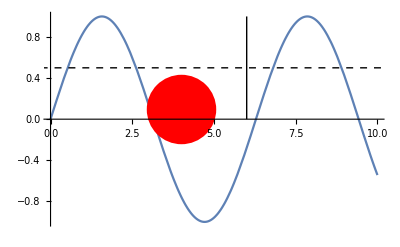

```mathematica
Plot[Sin[x],{x,0,10},Epilog->{Red,PointSize[.2],Point[{4,.1}],
Black,Line[{{6,0},{6,1}}],
Dashed,InfiniteLine[{0,.5},{1,0}]
}]
```

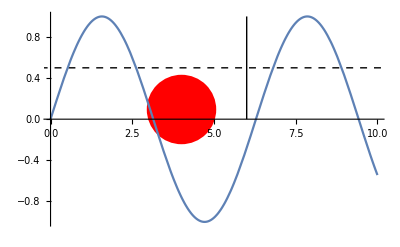

```mathematica
Plot[Sin[x],{x,0,10},Prolog->{Red,PointSize[.2],Point[{4,.1}],
Black,Line[{{6,0},{6,1}}],
Dashed,InfiniteLine[{0,.5},{1,0}]
},Method->{"AxesInFront" -> False}]
```

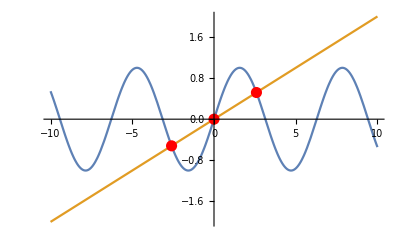

```mathematica
f1[x_]:=Sin[x];f2[x_]:=x/5;

sol=NSolve[f1[x]==f2[x],x,Reals];
list={x,f1[x]}/.sol;

Plot[{f1[x],f2[x]},{x,-10,10},PlotRange->{{-10,10},{-2,2}},Epilog->{Red,PointSize[.02],Point/@list}]
```

# Задача 3.3

```mathematica
F[r_]:=-1/r+1/r^2;
T=100;

sol=NDSolve[{
x''[t]==F[r] x[t]/r,y''[t]==F[r]y[t]/r,
x[0]==0,x'[0]==3/2,
y[0]==1,y'[0]==0
}/.r->√(x[t]^2+y[t]^2),{x,y},{t,0,T}]⟦1⟧;
```

```mathematica
Animate[
ParametricPlot[{x[t],y[t]}/.sol,{t,0,t1},PlotRange->8{{-1,1},{-1,1}}],
{t1,0.001,T}]
```

# Анимация

```mathematica
Graphics[{
Disk[{x[t],y[t]},.1]/.sol/.t->2
}
,PlotRange->8{{-1,1},{-1,1}}]
```

-Graphics-

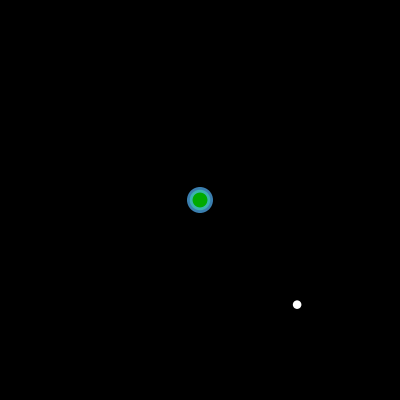

```mathematica
pic[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

pic[T/2]
```

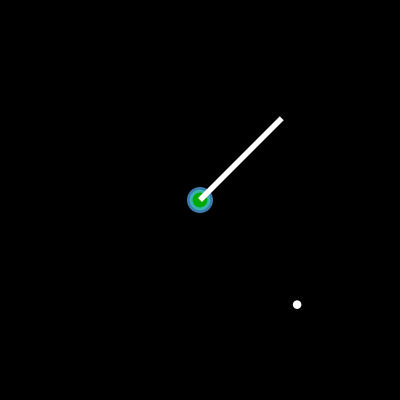

```mathematica
pic[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,Thickness[.01],Line[{{0,0},{4,4}}],
EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

pic[T/2]
```

```mathematica
pic[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,Thickness[.01],Line[{x[#],y[#]}/.sol&/@Subdivide[Max[t-10,0],t,100]],
EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

Animate[pic[t],{t,0,T}]
```

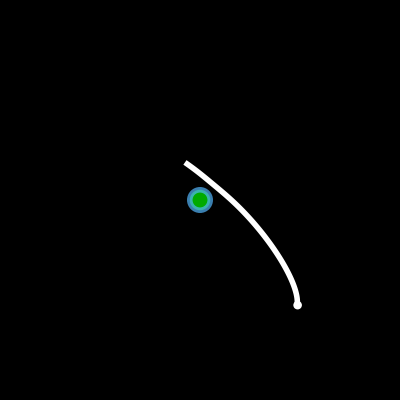

```mathematica
np=100;
pic[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,Thickness[.01],Line[{x[#],y[#]}/.sol&/@Subdivide[Max[t-10,0],t,np],VertexColors->(Opacity[#,White]&/@Subdivide[0,1,np])],
EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

img=pic[T/2]
```

# Экспорт

```mathematica
Directory[]
```

```mathematica
NotebookDirectory[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Directory[]
```

```mathematica
FileNames[]
```

```mathematica
Export["pic.pdf",img,"pdf"]
```

pic.pdf

```mathematica
Export["pic.png",img,"png"]
```

pic.png

```mathematica
Export["pic.png",img,"png",ImageSize->1000]
```

pic.png

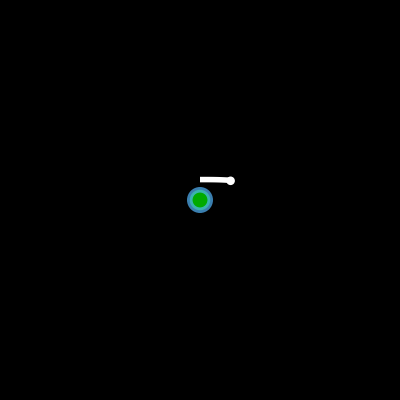

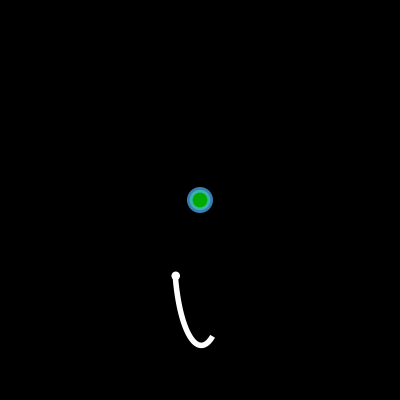

```mathematica
Pic[t_]:=pic[t T];
pic[1]
Pic[1]
```

```mathematica
(*Параметры анимации:*) 
dirname="animation_frames"; (*имя анимации*)
size=250; (*разрешение кадра в пикселях*)
time=5; (*время анимации в секундах*)
fps=25; (*частота кадров*)
loop=False;(*зациклевание анимации*)

(*Покадровый экспорт в .png:*) 
Nframes=Ceiling[fps time]; (*количество кадров*)
SetDirectory@NotebookDirectory[];
Quiet@CreateDirectory[dirname]; (*создание папки для сохранения кадров*)
Export[
dirname<>"//frame"<>StringPadLeft[ToString[#-1],4,"0"]<>".png",Rasterize[Pic[(#-1)/(Nframes-Boole[!loop])],ImageSize->size],"png"]&/@Range[Nframes];
```